```mathematica
Id[d_]:=IdentityMatrix[d];γe=1.76086 10^8;

σ={{1/2.({{0, 1}, {1, 0}}),1/2.({{0, -ⅈ}, {ⅈ, 0}}),1/2.({{1, 0}, {0, -1}})},{1/(√2.)({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}),1/(√2.)({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}}),({{1., 0, 0}, {0, 0, 0}, {0, 0, -1.}})}};

M1_⊗M2_:=KroneckerProduct[M1,M2]; M1_⊗M2_⊗M3_:=(M1⊗M2)⊗M3;

HyperfineHamiltonian[n_,spin_,hfc_]:=(
If[n==0,M=1; 
S=Table[σ[[1,p]],{p,3}]; Table[0,{2},{2}],
M=Product[spin[[k]],{k,1,n}]; II=Table[(Id[Product[spin[[k]],{k,1,j-1}]])⊗σ[[spin[[j]]-1,p]]⊗(Id[Product[spin[[k]],{k,j+1,n}]]),{j,n},{p,3}];
S=Table[σ[[1,p]]⊗Id[M],{p,3}];
Sum[hfc[[j,p,q]] σ[[1,p]]⊗II[[j,q]],{j,n},{p,3},{q,3}]  ]
);

ZeemanHamiltonian[ω0_,θ0_,ϕ0_]:=(
ω0(S[[1]] Sin[θ0]Cos[ϕ0]+S[[2]] Sin[θ0]Sin[ϕ0]+S[[3]] Cos[θ0])
);

TY[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(3*M))PT;
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

## Isotropic hyperfine coupling constants (HFCC) data for FADH^.

### Lee at el. (Alternative radical pairs for cryptochrome-based magnetoreception)

Nucleus | HFCC (mT)
H5 | -0.8029
N5 | 0.4313
H8(X3) | 0.2554
N10 | 0.2506
Hβ | 0.1908

## Figure 2d

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PAa=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Brown,Dotted},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PAb=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Magenta,DotDashed},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 5.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^5;
PAc=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.15,0.55},PlotRange->All,PlotStyle->{Cyan},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

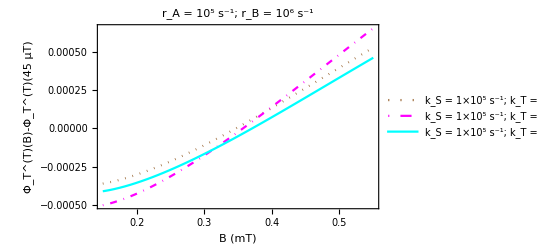

```mathematica
Show[PAa,PAb,PAc]
```

## Figure 3a

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PBa=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Brown,Dotted},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PBb=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Magenta,DotDashed},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 5.0×10^4s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^5;
PBc=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Cyan},PlotLegends->{"k_S = 1×10^5 s^-1; k_T = 1.0×10^5s^-1", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1"];
```

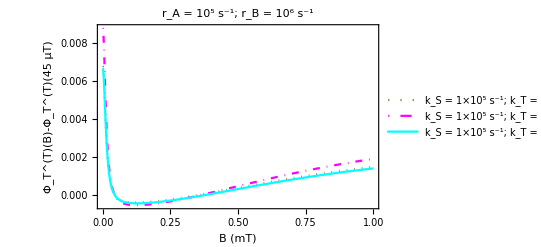

```mathematica
Show[PBa,PBb,PBc]
```

## Figure 5a

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PCa=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"0 mT", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.01, 0, 0}, {0, 0.01, 0}, {0, 0, 0.01}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PCb=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"0.01 mT", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.05, 0, 0}, {0, 0.05, 0}, {0, 0, 0.05}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PCc=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.06]},PlotStyle->{Red},PlotLegends->{"0.05 mT", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.1, 0, 0}, {0, 0.1, 0}, {0, 0, 0.1}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PCd=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"0.1 mT", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=1;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0.3, 0, 0}, {0, 0.3, 0}, {0, 0, 0.3}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PCe=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"0.3 mT", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

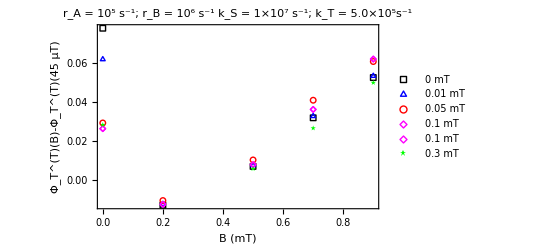

```mathematica
Show[PCa,PCb,PCc,PCd,PCd,PCe]
```

## Figure 5b

Fractional triplet yield was calculated using Advanced Research Computing (ARC) cluster at the University of Calgary. The obtained values are shown in the tables below.

### ks = 1.0*10^7; kt = 5.0*10^5;

```mathematica
nA=5;nB=0;
spinA={2,3,2,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.0 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.7 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.9 *γe,0,0,ks,kt,krA,krB];
```

```mathematica
{{B(mT), Subscript[Φ, T]^(T)(B)}, {0.0, 0.281780175}, {0.045, 0.202571888}, {0.2, 0.194541599}, {0.5, 0.207779569}, {0.7, 0.230570692}, {0.9, 0.249559271}}
```

```mathematica
change5a={{0,0.079208286},{0.2,-0.008030289},{0.5,0.005207681},{0.7,0.027998803},{0.9,0.046987383}};PDa=ListPlot[change5a,PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"5 HFI (H5, N5, 3 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=4;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PDb=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"4 HFI (H5, N5, 2 X Hβ)"},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PDc=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"3 HFI (H5, N5, 1 X Hβ)"},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,3,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2506, 0, 0}, {0, 0.2506, 0}, {0, 0, 0.2506}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PDd=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Cyan},PlotLegends->{"3 HFI (H5, N5, N10)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PDe=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"2 HFI (H5, N5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PDf=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red},PlotLegends->{"1 HFI (H5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

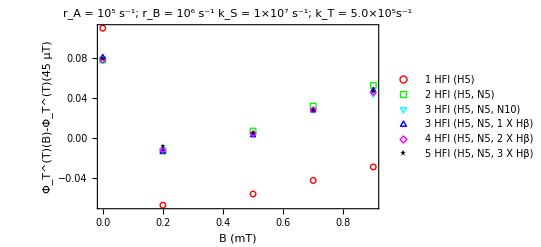

```mathematica
Show[PDf,PDe,PDd,PDc,PDb,PDa]
```

## Figure 5c

```mathematica
TYEx[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_,J_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB-J*γe*(SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]]);
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(3*M))PT;
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

```mathematica
nA=2;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
J=0.0;
PEa=Plot[(TYEx[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,J]-TYEx[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,J]),{B,0.0,0.9},PlotRange->All,PlotStyle->Green, PlotLegends ->{"J = 0.0 mT",Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold, 13],PlotLabel->"r_A=10^5 s^-1; r_B=10^6 s^-1
k_T=5.0×10^5s^-1, k_S=1.0×10^7s^-1"];
```

```mathematica
nA=2;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
J=0.1;
PEb=Plot[(TYEx[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,J]-TYEx[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,J]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Blue,Dotted}, PlotLegends ->{"J = 0.1 mT",Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold, 13],PlotLabel->"r_A=10^5 s^-1; r_B=10^5 s^-1
k_T=5.0×10^5s^-1, k_S=1.0×10^7s^-1"];
```

```mathematica
nA=2;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
J=0.3;
PEc=Plot[(TYEx[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,J]-TYEx[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,J]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Red,Dashed}, PlotLegends ->{"J = 0.3 mT",Line},FrameLabel ->{"B (mT)","% change in Φ_T^(T)(relative to 45 μT)" },Frame->True,LabelStyle -> Directive[ Bold, 13],PlotLabel->"r_A=10^5 s^-1; r_B=10^5 s^-1
k_T=5.0×10^5s^-1, k_S=1.0×10^7s^-1"];
```

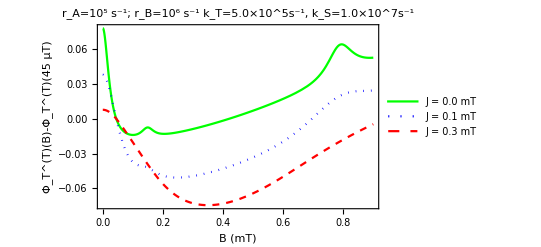

```mathematica
Show[PEa,PEb,PEc]
```

## Figure 5d

```mathematica
TYDD[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_,r_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB-(2/3)*(2.78/r^3)*γe*(-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]+2*SA[[3]]⊗SB[[3]]);
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(3*M))PT;
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PFa=Plot[(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Blue},PlotLegends->{"∞", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1*10^7 s^-1; k_T = 1*10^6 s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
r=1;
PFb=Plot[(TYDD[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,r]-TYDD[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,r]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Brown},PlotLegends->{"1 nm", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1*10^7 s^-1; k_T = 1*10^6 s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
r=2;
PFc=Plot[(TYDD[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,r]-TYDD[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,r]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Purple},PlotLegends->{"2 nm", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1*10^7 s^-1; k_T = 1*10^6 s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
r=3;
PFd=Plot[(TYDD[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,r]-TYDD[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,r]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Red},PlotLegends->{"3 nm", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1*10^7 s^-1; k_T = 1*10^6 s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
r=4;
PFe=Plot[(TYDD[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,r]-TYDD[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,r]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Green},PlotLegends->{"4 nm", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1*10^7 s^-1; k_T = 1*10^6 s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
r=5;
PFf=Plot[(TYDD[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB,r]-TYDD[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB,r]),{B,0.0,0.9},PlotRange->All,PlotStyle->{Orange},PlotLegends->{"5 nm", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1*10^7 s^-1; k_T = 1*10^6 s^-1"];
```

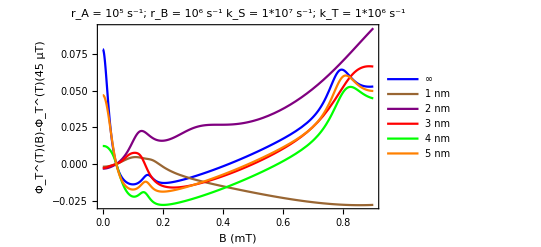

```mathematica
Show[PFa,PFb,PFc,PFd,PFe,PFf]
```

## Figure 5e

```mathematica
no = 100;
U = RandomReal[{0,1},no];
V = RandomReal[{0,1},no];
Theta = Table[ArcCos[2*v-1],{v,V}];
Phi = Table[2*Pi*u,{u,U}];
X =Table[Sin[Theta[[i]]]*Cos[Phi[[i]]],{i,no}];
Y =Table[Sin[Theta[[i]]]*Sin[Phi[[i]]],{i,no}];
Z =Table[Cos[Theta[[i]]],{i,no}];
pts =Transpose[{X,Y,Z}];
Graphics3D[{Point[pts]},Boxed->True]
```

-Graphics3D-

```mathematica
nA=2;nB=0;
spinA={2,3};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe; 
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PGa=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.025,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.05]},PlotStyle->{Blue}, PlotLegends ->{"Isotropic HFI",Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3};
aisohfcA={({{-1.3794, -0.0387, 0.0046}, {-0.0387, -0.0822, -0.0833}, {0.0046, -0.0833, -0.9472}}),({{-0.0906, 0.0028, -0.0036}, {0.0028, -0.0799, 0.1383}, {-0.0036, 0.1383, 1.4645}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 5.0*10^5;
PGb=ListPlot[Table[{B,(((Sum[TY[nA,spinA,aisohfcA,nB,spinB,hfcB,B*γe,Theta[[i]],Phi[[i]],ks,kt,krA,krB],{i,1,no}]/no))-((Sum[TY[nA,spinA,aisohfcA,nB,spinB,hfcB,0.045*γe,Theta[[i]],Phi[[i]],ks,kt,krA,krB],{i,1,no}]/no)))},{B,{0,0.025,0.05,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red}, PlotLegends ->{"Anisotropic HFI
(average over 100 random directions)",Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 5.0×10^5s^-1"];
```

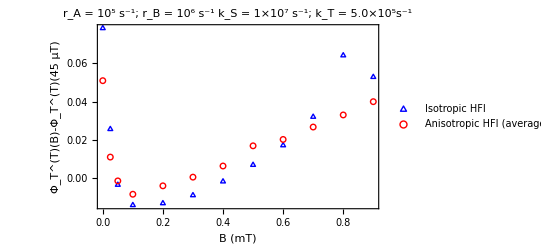

```mathematica
Show[PGa,PGb]
```

# Supporting Information

## Figure 1

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PHa=ContourPlot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2*γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^5 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourLines->False,ContourShading->{ColorData["Legacy"]["Violet"],ColorData["Legacy"]["Steelblue"],ColorData["Legacy"]["CadetBlue"],ColorData["Legacy"]["Olive"],ColorData["Legacy"]["DarkKhaki"],ColorData["Legacy"]["Goldenrod"],ColorData["Legacy"]["YellowOchre"]},Contours->{-3,-6,-9,-12,-15,-18}];
```

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PHb=ContourPlot[100*(TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5*γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^6 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourShading->None,ContourStyle->Directive[Thick,White,Dashed],Contours->{0.5,0,-2,-5,-15},Epilog->{Text[Framed[ToString[-15],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[7*10^6],Log[1*10^5]}],Text[Framed[ToString[-5],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[4.5*10^6],Log[3*10^6]}],Text[Framed[ToString[-2],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2.3*10^6],Log[4*10^6]}],Text[Framed[ToString[0],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2.0*10^5],Log[5*10^5]}],Text[Framed[ToString[0.5],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[9*10^5],Log[1.0*10^5]}]}];
```

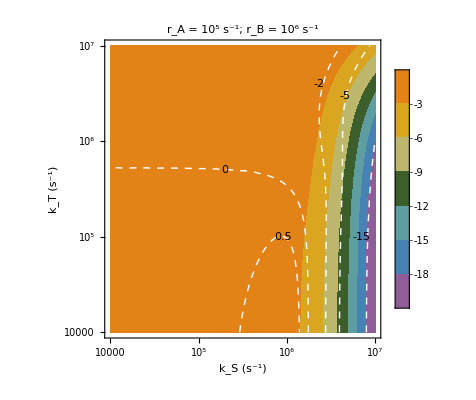

```mathematica
Show[PHb,PHa,PHb]
```

## Figure 4b

```mathematica
TYFP[nA_,spinA_,hfcA_,nB_,spinB_,hfcB_,ω0_,θ0_,ϕ0_,ks_,kt_,krA_,krB_]:=(
HA=HyperfineHamiltonian[nA,spinA,hfcA]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MA=M;SA=S//Chop;
HB=HyperfineHamiltonian[nB,spinB,hfcB]+ZeemanHamiltonian[ω0,θ0,ϕ0];
MB=M;SB=S//Chop;
M=MA MB;
H=HA⊗Id[2 MB]+Id[2 MA]⊗HB;
PS=0.25 Id[4 M]-SA[[1]]⊗SB[[1]]-SA[[2]]⊗SB[[2]]-SA[[3]]⊗SB[[3]];
PT=0.75 Id[4 M]+SA[[1]]⊗SB[[1]]+SA[[2]]⊗SB[[2]]+SA[[3]]⊗SB[[3]];
IS = (1/(4*M))Id[4M];
ISV=Transpose[{Flatten[IS]}];
KK=(ks/2)*(PS⊗Id[4M]+Id[4M]⊗Transpose[PS])+(kt/2)*(PT⊗Id[4M]+Id[4M]⊗Transpose[PT]);
RR=krA*((3/4)*(Id[4M]⊗Id[4M])-SA[[1]]⊗Id[2MB]⊗Transpose[SA[[1]]⊗Id[2MB]]-SA[[2]]⊗Id[2MB]⊗Transpose[SA[[2]]⊗Id[2MB]]-SA[[3]]⊗Id[2MB]⊗Transpose[SA[[3]]⊗Id[2MB]])+krB*((3/4)*(Id[4M]⊗Id[4M])-Id[2MA]⊗SB[[1]]⊗Transpose[Id[2MA]⊗SB[[1]]]-Id[2MA]⊗SB[[2]]⊗Transpose[Id[2MA]⊗SB[[2]]]-Id[2MA]⊗SB[[3]]⊗Transpose[Id[2MA]⊗SB[[3]]]);
HH=H⊗Id[4 M]-Id[4 M]⊗Transpose[H];
LL=ⅈ*HH+KK+RR;
rhov =Inverse[LL].ISV;
rho = ArrayReshape[rhov,{4M,4M}];
kt*Re[Tr[PT.rho]]//Chop  
);
```

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PIa=ContourPlot[100*(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.2*γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^5 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourLines->False,ContourShading->{ColorData["Legacy"]["Violet"],ColorData["Legacy"]["Steelblue"],ColorData["Legacy"]["CadetBlue"],ColorData["Legacy"]["Olive"],ColorData["Legacy"]["DarkKhaki"],ColorData["Legacy"]["Goldenrod"],ColorData["Legacy"]["YellowOchre"]},Contours->{0,-3,-6,-9,-12,-15}];
```

```mathematica
spinA={2};
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}})}γe;
nA=1;nB=0;
krA=1.0*10^5;krB=1.0*10^6;
PIb=ContourPlot[100*(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.5*γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB])/TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045*γe,0,0,ks,kt,krA,krB],{ks,1.0* 10^4,1.0* 10^7},{kt,1.0* 10^4,1.0* 10^7},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic,FrameLabel ->{"k_S (s^-1)","k_T (s^-1)"}, PlotLabel ->"r_A = 10^5 s^-1; r_B = 10^6 s^-1",LabelStyle -> Directive[ Bold],PlotRange->All,ContourShading->None,ContourStyle->Directive[Thick,White,Dashed],Contours->{-15,-5,-0.01,0,0.1,2},Epilog->{Text[Framed[ToString[-8],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[8*10^6],Log[5*10^4]}],Text[Framed[ToString[-4],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[6*10^6],Log[5*10^5]}],Text[Framed[ToString[-0.01],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[5.1*10^4],Log[3*10^5]}],Text[Framed[ToString[-0.01],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[1.3*10^6],Log[5*10^5]}],Text[Framed[ToString[0],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[4.3*10^5],Log[4.5*10^5]}],Text[Framed[ToString[0.1],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[1*10^5],Log[2*10^6]}],Text[Framed[ToString[0.1],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[5*10^5],Log[2*10^5]}],Text[Framed[ToString[2],FrameStyle->None,Background->None,BaseStyle->{Bold,14}],{Log[2.4*10^6],Log[6.2*10^6]}]}];
```

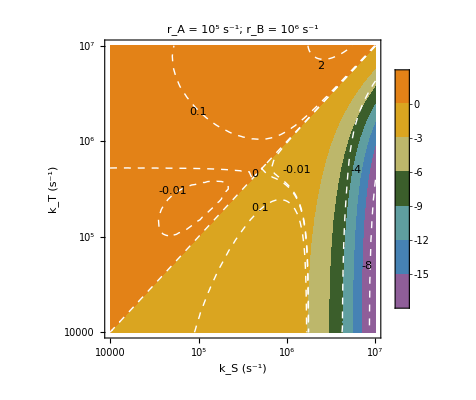

```mathematica
Show[PIb,PIa,PIb]
```

## Figure 3

```mathematica
nA=1;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 1.0*10^4;
PJa=Plot[(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Brown,Dotted}, PlotLegends ->{"k_T = 1.0×10^4s^-1",Line},FrameLabel ->{"B (mT)","Φ_T(B)- Φ_T(45 μT)" },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^5 s^-1"];
```

```mathematica
nA=1;nB=0;
hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}})}γe;
spinA={2,3};
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^5; kt = 5.0*10^4;
PJb=Plot[(TYFP[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TYFP[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB]),{B,0.0,1.0},PlotRange->All,PlotStyle->{Magenta,DotDashed}, PlotLegends ->{"k_T = 5.0×10^4s^-1",Line},FrameLabel ->{"B (mT)","% change in Φ_T^(T)(relative to 45μT)" },Frame->True,LabelStyle -> Directive[ Bold]];
```

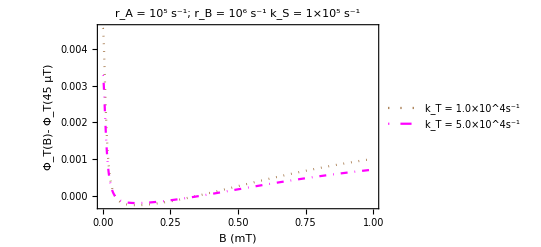

```mathematica
Show[PJa,PJb]
```

## Figure 4 a

Following Fractional triplet yield was calculated using Advanced Research Computing (ARC) cluster at the University of Calgary. The obtained values are shown in the tables below.

### ks = 1.0*10^7; kt = 1.0*10^6;

```mathematica
nA=5;nB=0;
spinA={2,3,2,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.0 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.7 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.9 *γe,0,0,ks,kt,krA,krB];
```

```mathematica
{{B(mT), Subscript[Φ, T]^(T)(B)}, {0.0, 0.40692811}, {0.045, 0.324567391}, {0.2, 0.3105352}, {0.5, 0.326882527}, {0.7, 0.356003429}, {0.9, 0.378919939}}
```

```mathematica
change5b={{0,0.082360719},{0.2,-0.01403219},{0.5,0.002315136},{0.7,0.031436038},{0.9,0.054352548}};PKa=ListPlot[change5b,PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"5 HFI (H5, N5, 3 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=4;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
PKb=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"4 HFI (H5, N5, 2 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
PKc=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"3 HFI (H5, N5, 1 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,3,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2506, 0, 0}, {0, 0.2506, 0}, {0, 0, 0.2506}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
PKd=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Cyan},PlotLegends->{"3 HFI (H5, N5, N10)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
PKe=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"2 HFI (H5, N5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 1.0*10^7; kt = 1.0*10^6;
PKf=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red},PlotLegends->{"1 HFI (H5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 1×10^7 s^-1; k_T = 1.0×10^6s^-1"];
```

```mathematica
Show[PKf,PKe,PKd,PKc,PKb,PKa]
```

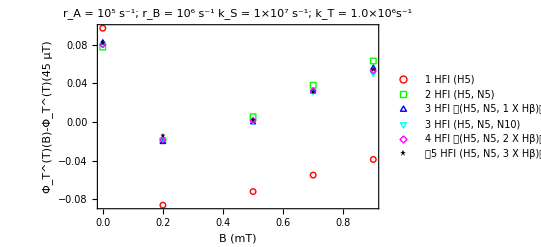

## Figure 4 a

Following Fractional triplet yield was calculated using Advanced Research Computing (ARC) cluster at the University of Calgary. The obtained values are shown in the tables below.

### ks = 5.0*10^6; kt = 2.0*10^6;

```mathematica
nA=5;nB=0;
spinA={2,3,2,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.0 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.2 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.5 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.7 *γe,0,0,ks,kt,krA,krB];
TY[nA,spinA,hfcA,nB,spinB,hfcB,0.9 *γe,0,0,ks,kt,krA,krB];
```

```mathematica
{{B(mT), Subscript[Φ, T]^(T)(B)}, {0.0, 0.650393252}, {0.045, 0.601898111}, {0.2, 0.594458218}, {0.5, 0.60496605}, {0.7, 0.623153826}, {0.9, 0.636510445}}
```

```mathematica
change5c={{0,0.048495141},{0.2,-0.007439893},{0.5,0.003067939},{0.7,0.021255715},{0.9,0.034612334}};PLa=ListPlot[change5c,PlotRange->All,PlotMarkers->{"★",PointSize[0.06]},PlotStyle->{Black},PlotLegends->{"5 HFI (H5, N5, 3 X Hβ)"},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
nA=4;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
PLb=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"◇",PointSize[0.06]},PlotStyle->{Magenta},PlotLegends->{"4 HFI (H5, N5, 2 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
PLc=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"△",PointSize[0.06]},PlotStyle->{Blue},PlotLegends->{"3 HFI (H5, N5, 1 X Hβ)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
nA=3;nB=0;
spinA={2,3,3,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2506, 0, 0}, {0, 0.2506, 0}, {0, 0, 0.2506}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
PLd=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"▽",PointSize[0.06]},PlotStyle->{Cyan},PlotLegends->{"3 HFI (H5, N5, N10)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
nA=2;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;
PLe=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"□",PointSize[0.06]},PlotStyle->{Green},PlotLegends->{"2 HFI (H5, N5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^□s^-1"];
```

```mathematica
nA=1;nB=0;
spinA={2,3,2,2};hfcA={({{-0.8029, 0, 0}, {0, -0.8029, 0}, {0, 0, -0.8029}}),({{0.4313, 0, 0}, {0, 0.4313, 0}, {0, 0, 0.4313}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}}),({{0.2554, 0, 0}, {0, 0.2554, 0}, {0, 0, 0.2554}})}γe;
spinB={2};hfcB={({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})}γe; 
krA=1.0*10^5;krB=1.0*10^6;
ks = 5.0*10^6; kt = 2.0*10^6;;
PLf=ListPlot[Table[{B,(TY[nA,spinA,hfcA,nB,spinB,hfcB,B *γe,0,0,ks,kt,krA,krB]-TY[nA,spinA,hfcA,nB,spinB,hfcB,0.045 *γe,0,0,ks,kt,krA,krB])},{B,{0,0.2,0.5,0.7,0.9}}],PlotRange->All,PlotMarkers->{"○",PointSize[0.05]},PlotStyle->{Red},PlotLegends->{"1 HFI (H5)", Line},FrameLabel ->{"B (mT)","Φ_T^(T)(B)-Φ_T^(T)(45 μT)"  },Frame->True,LabelStyle -> Directive[ Bold,13],PlotLabel->"r_A = 10^5 s^-1; r_B = 10^6 s^-1
k_S = 5×10^6 s^-1; k_T = 2.0×10^6s^-1"];
```

```mathematica
Show[PLf,PLe,PLd,PLc,PLb,PLa]
```